```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\USERS\Guokr\Documents\GitHub\WhyMathematica\DataVisualization\Other\Exoplanet

## Exoplanet Dashboard

```mathematica
exoDataDashboard=Import["Data/exoDataDashboard.txt","CSV"]
```

{{NAME,A,ECC,PER,MSINI,MASS,FE,MSTAR,DATE,R,GRAVITY,DENSITY,DIST,DEC},{,au,,day,mjupiter,mearth,,msun,,rjupiter,,g/cm^3,pc,deg},«3313»,{KOI 597.01,0.133,0,17.3069,,7.44537,,,,0.236418,,,,},{KOI 730.04,0.073,0,7.38402,,2.77063,,,,0.146311,,,,}}

```mathematica
exoDataDashboard[[3]]
```

{WASP-57 b,0.0386362,0,2.83897,0.675475,,-0.25,0.954,2013,0.916,,0.11576,455,-2.05764}

```mathematica
lenDB=Length[exoDataDashboard]
```

3317

```mathematica
lenDB2=Min[Table[Length[exoDataDashboard[[i]]],{i,1,lenDB}]]
```

14

Show the first seven exoplanets in a grid

```mathematica
Grid[Table[exoDataDashboard[[i]],{i,1,10}]]
```

NAME | A | ECC | PER | MSINI | MASS | FE | MSTAR | DATE | R | GRAVITY | DENSITY | DIST | DEC
 | au |  | day | mjupiter | mearth |  | msun |  | rjupiter |  | g/cm^3 | pc | deg
WASP-57 b | 0.0386362 | 0 | 2.83897 | 0.675475 |  | -0.25 | 0.954 | 2013 | 0.916 |  | 0.11576 | 455 | -2.05764
HATS-1 b | 0.0444708 | 0.12 | 3.44646 | 1.85957 | 592.75 | -0.06 | 0.986 | 2013 | 1.302 | 3.43517 | 1.03 | 303 | -23.3548
HD 77338 b | 0.0612143 | 0.09 | 5.7361 | 0.0498139 | 15.8317 | 0.35 | 0.93 | 2013 |  |  |  | 40.7498 | -25.5264
Kepler-58 c | 0.119982 |  | 15.5742 |  |  |  | 0.95 | 2013 | 0.254925 |  |  |  | 39.115
HD 4732 c | 4.60219 | 0.23 | 2732 | 2.36493 | 751.614 | 0.01 | 1.74 | 2013 |  |  |  | 57.9039 | -24.1365
Kepler-62 c | 0.0928559 | 0.186815 | 12.4417 |  | 0 | -0.37 | 0.69 | 2013 | 0.0481326 |  |  | 368 | 45.3499
WASP-52 b | 0.0271336 | 0 | 1.74978 | 0.45566 | 145.295 | 0.03 | 0.87 | 2013 | 1.27 | 2.84909 | 0.29172 | 140 | 8.76128
Kepler-60 b | 0.0750769 |  | 7.13162 |  |  |  | 1.11 | 2013 | 0.203227 |  |  |  | 42.265

Test plot

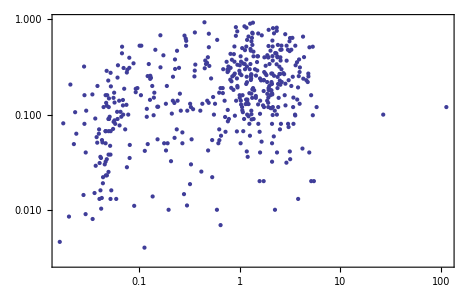

```mathematica
ListLogLogPlot[Table[{exoDataDashboard[[i]][[2]],exoDataDashboard[[i]][[3]]},{i,3,lenDB}],Frame->True]
```

Remove the data of year founded. Polished data table.

```mathematica
exoDataDBP=Table[Delete[exoDataDashboard[[i]],9],{i,1,lenDB}]
```

{{NAME,A,ECC,PER,MSINI,MASS,FE,MSTAR,R,GRAVITY,DENSITY,DIST,DEC},{,au,,day,mjupiter,mearth,,msun,rjupiter,,g/cm^3,pc,deg},{WASP-57 b,0.0386362,0,2.83897,0.675475,,-0.25,0.954,0.916,,0.11576,455,-2.05764},{HATS-1 b,0.0444708,0.12,3.44646,1.85957,592.75,-0.06,0.986,1.302,3.43517,1.03,303,-23.3548},{HD 77338 b,0.0612143,0.09,5.7361,0.0498139,15.8317,0.35,0.93,,,,40.7498,-25.5264},«3308»,{KOI 730.03,0.14,0,19.7213,,6.60323,,,0.223035,,,,},{KOI 111.03,0.253,0,51.7563,,5.86406,,,0.210545,,,,},{KOI 597.01,0.133,0,17.3069,,7.44537,,,0.236418,,,,},{KOI 730.04,0.073,0,7.38402,,2.77063,,,0.146311,,,,}}

```mathematica
lenDBP=Length[exoDataDBP]
lenDBP2=Length[exoDataDBP[[1]]]
```

3317

13

To examing the data data rules of Table

```mathematica
Table[{j,i},{i,1,5},{j,1,5}]
Insert[%,,{1,,1}]
```

{{{1,1},{2,1},{3,1},{4,1},{5,1}},{{1,2},{2,2},{3,2},{4,2},{5,2}},{{1,3},{2,3},{3,3},{4,3},{5,3}},{{1,4},{2,4},{3,4},{4,4},{5,4}},{{1,5},{2,5},{3,5},{4,5},{5,5}}}

Part::pspec: Part specification i is neither an integer nor a list of integers.

Insert::psl: Position specification {1, Null, 1} in Insert[{{{1, 1}, {2, 1}, {3, 1}, {4, 1}, {5, 1}}, {{1, 2}, {2, 2}, {3, 2}, {4, 2}, {5, 2}}, {{1, 3}, {2, 3}, {3, 3}, {4, 3}, {5, 3}}, {{1, 4}, {2, 4}, {3, 4}, {4, 4}, {5, 4}}, {{1, 5}, {2, 5}, {3, 5}, {4, 5}, {5, 5}}}, {"Name", "Semi-Major Axis", "Eccentricity", "Period", "Mass(/Jupter)", "Mass(/Earth)", "Metallity", "Star Mass", "Radius", "Gravity", "Density", "Distance", "Inclination"} ⟦ i ⟧, {1, Null, 1}] is not an integer or a list of integers.

Insert[{{{1,1},{2,1},{3,1},{4,1},{5,1}},{{1,2},{2,2},{3,2},{4,2},{5,2}},{{1,3},{2,3},{3,3},{4,3},{5,3}},{{1,4},{2,4},{3,4},{4,4},{5,4}},{{1,5},{2,5},{3,5},{4,5},{5,5}}},{Name,Semi-Major Axis,Eccentricity,Period,Mass(/Jupter),Mass(/Earth),Metallity,Star Mass,Radius,Gravity,Density,Distance,Inclination}⟦i⟧,{1,Null,1}]

Create the Grid Head table

```mathematica
head={"","Semi-Major Axis","Eccentricity","Period","Mass(/Jupter)","Mass(/Earth)","Metallity","Star Mass","Radius","Gravity","Density","Distance","Inclination"}
```

{,Semi-Major Axis,Eccentricity,Period,Mass(/Jupter),Mass(/Earth),Metallity,Star Mass,Radius,Gravity,Density,Distance,Inclination}

```mathematica
Table[head[[i]],{i,1,Floor[lenDBP2/2]}]
```

{,Name,Semi-Major Axis,Eccentricity,Period,Mass(/Jupter)}

```mathematica
plt1=Table[ListLogLogPlot[Table[{exoDataDBP[[n]][[j]],exoDataDBP[[n]][[i]]},{n,3,lenDBP}],Frame->True],{i,2,Floor[lenDBP2/2]},{j,2,Floor[lenDBP2/2]}];
plt2=Table[ListLogLogPlot[Table[{exoDataDBP[[n]][[j]],exoDataDBP[[n]][[i]]},{n,3,lenDBP}],Frame->True],{i,Floor[lenDBP2/2]+1,lenDBP2},{j,Floor[lenDBP2/2]+1,lenDBP2}];
```

Add heads to table

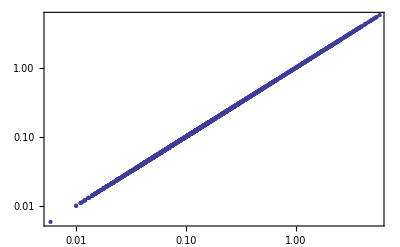
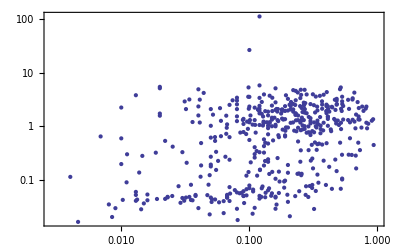
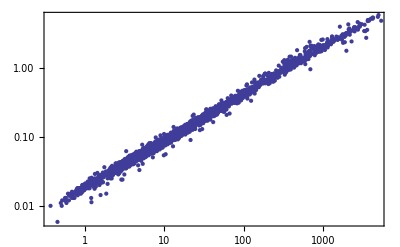
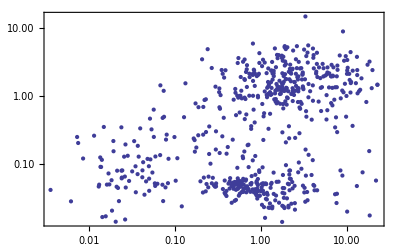
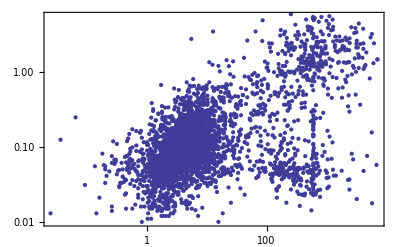

```mathematica
plt1[[1]]
```

```mathematica
plt1Mod=Prepend[Table[Prepend[plt1[[i]],head[[i+1]]],{i,1,Length[plt1[[1]]]}],Table[head[[i]],{i,1,Length[plt1[[1]]]+1}]];
```

```mathematica
plt2Mod=Prepend[Table[Prepend[plt2[[i]],head[[i+Length[plt1[[1]]]+1]]],{i,1,Length[head]-Length[plt1[[1]]]-1}],Table[head[[i]],{i,Length[plt1[[1]]]+1,Length[head]}]];
```

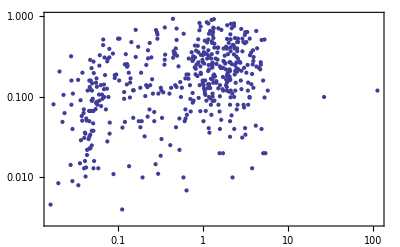
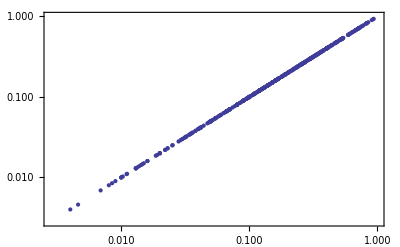
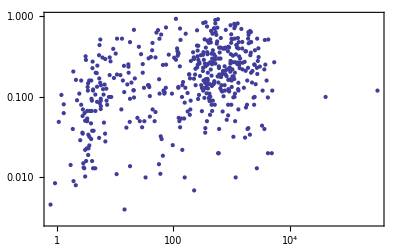
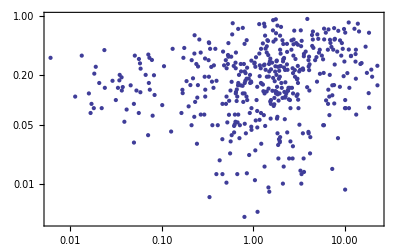
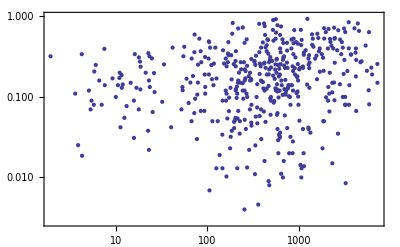
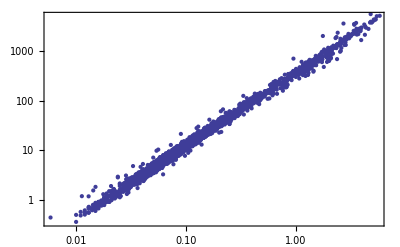
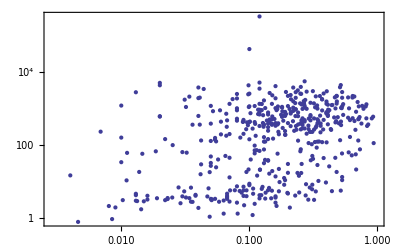
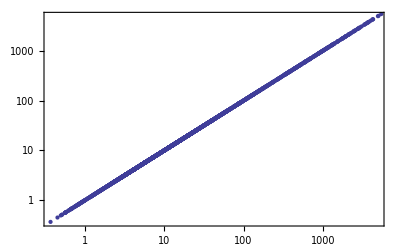
| Semi-Major Axis | Eccentricity | Period | Mass(/Jupter) | Mass(/Earth)
Semi-Major Axis | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Eccentricity | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Period | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Mass(/Jupter) | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Mass(/Earth) | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[plt1Mod]
```

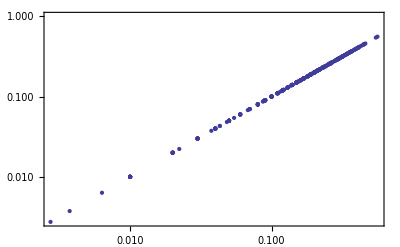
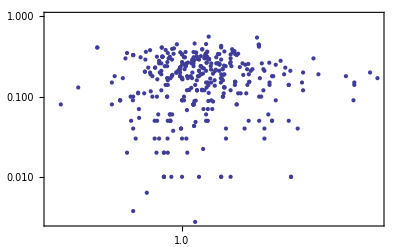
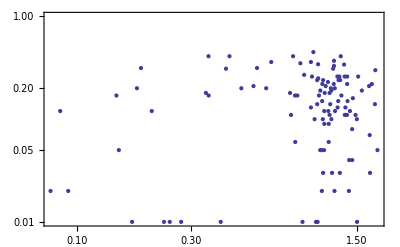
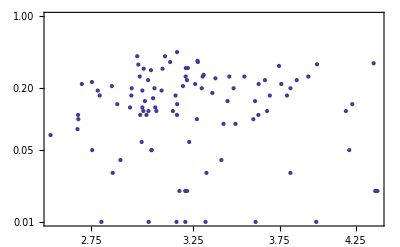
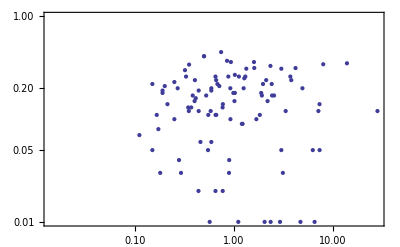
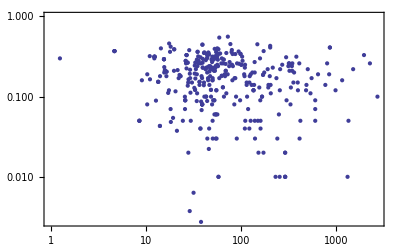
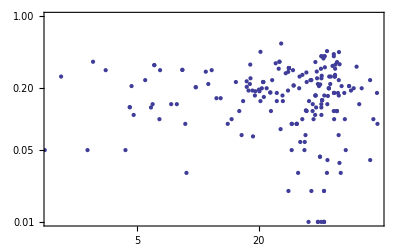
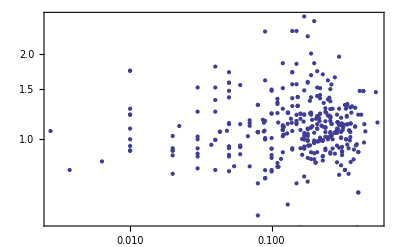
Mass(/Earth) | Metallity | Star Mass | Radius | Gravity | Density | Distance | Inclination
Metallity | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Star Mass | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Radius | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Gravity | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Density | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Distance | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Inclination | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[plt2Mod]
```

## Play With Exoplanet Default Table

```mathematica
exoData=Import["Data/ExoplanetDefaultTable.txt","CSV"]
```

{{NAME,MSINI,A,PER,ECC,OM,T0,K,MSTAR},{,mjupiter,au,day,,deg,jd,m/s,msun},{WASP-14 b,7.65457,0.0367693,2.24375,0.091,253.371,2.45446×10^6,993,1.31},{Kepler-50 b,,0.0825598,7.81251,,,,,1.23},«3309»,{KOI 730.02,,0.088,9.84871,0,,,,},{KOI 730.03,,0.14,19.7213,0,,,,},{KOI 111.03,,0.253,51.7563,0,,,,},{KOI 730.04,,0.073,7.38402,0,,,,}}

```mathematica
exoData[[3]]
```

{WASP-14 b,7.65457,0.0367693,2.24375,0.091,253.371,2.45446×10^6,993,1.31}

```mathematica
len=Length[exoData]
```

3317

```mathematica
Grid[exoData];
```

### Try To Visualize the Mass of planets(2), Semi-Axis of planets(3),Mass of star(9).

```mathematica
visDataMSM=Table[{exoData[[i]][[2]],exoData[[i]][[3]],exoData[[i]][[9]]},{i,3,len}]
```

{{7.65457,0.0367693,1.31},{,0.0825598,1.23},{0.0266149,0.0453704,0.912},{0.615135,0.0399488,0.92},{2.1395,1.74607,1.58},{0.0622185,0.0515012,1.24},{0.04247,0.106504,0.95},{3.3748,0.494668,0.9},{0.300201,0.0521087,1.01},{0.0477376,0.119192,0.933},{0.578118,0.0473714,1},{4.02189,4.92406,1.18},«3291»,{,0.116,},{,0.264,},{,0.046,},{,0.172,},{,0.15,},{,0.087,},{,0.075,},{,0.116,},{,0.088,},{,0.14,},{,0.253,},{,0.073,}}

```mathematica
DeleteCases
```

```mathematica
visDataMSM[[2]]
Length[%]
```

{,0.0825598,1.23}

3

```mathematica
BubbleChart[visDataMSM,ChartBaseStyle->{EdgeForm[None],Opacity[0.4]}]
```

-Graphics-

```mathematica
visBubble1=BubbleChart[visDataMSM,ChartBaseStyle->{EdgeForm[None],Opacity[0.2]},PlotRange->{Full,{-2,16}},BubbleSizes->{0.005,0.01}]
```

-Graphics-

```mathematica
visBubble1Rev=Show[visBubble1,FrameLabel-{"Mass of Planets","Semiaxis of Planets"},PlotLabel->"Visualization of Exoplanets | Bubble Size: Mass of Star"]
```